```mathematica
table=Import["C:\\Users\\Andrey\\Desktop\\ArHeSpectrum_GUIversion\\freqs.csv"];
model=ω0+Sum[Subscript[c, 6j] r^(-6j),{j,1,6}];
coeffs=Table[FindFit[Table[{table[[i,1]],table[[i,j]]},{i,1,Length[table]}],model,{ω0,Subscript[c, 6],Subscript[c, 12],Subscript[c, 18],Subscript[c, 24],Subscript[c, 30],Subscript[c, 36]},r],{j,2,Length[table[[1]]]}];
```

```mathematica
Manipulate[Show[ListPlot[Table[{table[[i,1]],table[[i,j]]},{i,1,Length[table]}],PlotRange->Full],Plot[model/.coeffs[[j-1]],{r,2 10^-8,10^-7},PlotRange->Full]],{j,2,Length[table[[1]]],1}]
```

```mathematica
k=Table[Table[coeffs[[i,j,2]],{j,2,Length[coeffs[[1]]]}],{i,1,Length[coeffs]}];
```

```mathematica
ω=Table[coeffs[[i,1,2]],{i,1,Length[coeffs]}];
```

```mathematica
n=Table[(Gamma[(6i-1)/2] √π)/Gamma[(6i)/2],{i,1,6}];
μ=40/11;
R=8.31 10^7;
f[v_,T_]:=(μ/(4π R T))^(3/2)4π v^2 ⅇ^(-(μ v^2)/(2 R T));
η[c_,r_,v_]:=Sum[(c[[i]] n[[i]])/v r^(1-6i),{i,1,6}];
integrand[c_,r_,v_,T_]:= r v(1-Cos[η[c,r,v]]+ⅈ Sin[η[c,r,v]])f[v,T];
```

```mathematica
Parallelize[Table[NIntegrate[integrand[k[[j]],r,v,300],{r,2 10^-8,10^-5},{v,10^3,10^6},Method->"LevinRule",PrecisionGoal->4],{j,1,Length[k]}]]
```

{1.24507×10^-10-9.73458×10^-11 ⅈ,1.28414×10^-10-1.00183×10^-10 ⅈ,1.28623×10^-10-1.00333×10^-10 ⅈ,1.31708×10^-10-1.02572×10^-10 ⅈ,1.16365×10^-10-9.14184×10^-11 ⅈ,1.20947×10^-10-9.47506×10^-11 ⅈ,1.28414×10^-10-1.00183×10^-10 ⅈ,1.28489×10^-10-1.00235×10^-10 ⅈ,1.31708×10^-10-1.02572×10^-10 ⅈ,1.16519×10^-10-9.15307×10^-11 ⅈ,1.20947×10^-10-9.47506×10^-11 ⅈ,1.28623×10^-10-1.00333×10^-10 ⅈ,1.16365×10^-10-9.14184×10^-11 ⅈ,1.28489×10^-10-1.00235×10^-10 ⅈ,1.16519×10^-10-9.15307×10^-11 ⅈ,1.336×10^-10-1.03949×10^-10 ⅈ,1.22693×10^-10-9.60221×10^-11 ⅈ,1.336×10^-10-1.03949×10^-10 ⅈ,1.22693×10^-10-9.60221×10^-11 ⅈ,1.27752×10^-10-9.9702×10^-11 ⅈ,1.27752×10^-10-9.9702×10^-11 ⅈ,1.24865×10^-10-9.76068×10^-11 ⅈ,1.29301×10^-10-1.0083×10^-10 ⅈ,1.01355×10^-10-8.04925×10^-11 ⅈ,1.01355×10^-10-8.04925×10^-11 ⅈ,9.54203×10^-11-7.61544×10^-11 ⅈ,1.0257×10^-10-8.13838×10^-11 ⅈ}

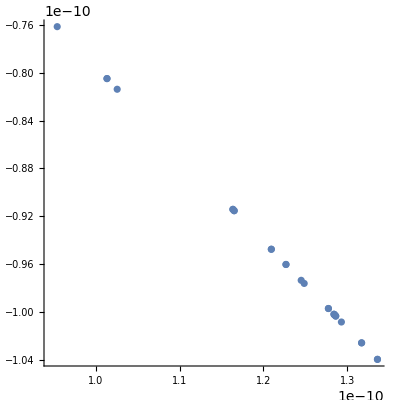

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%76,AspectRatio->1]
```